```mathematica
SetDirectory[NotebookDirectory[]]
<<anybubble.m
<<powell.m
Options[FindBubble]
```

/Users/fujikurakouhei/Dropbox/EWBG/Results

{Verbose→False,SpaceTimeDimension→3,StartAnalyticFraction→1/100,EndAnalyticFraction→1/100,MaxIntervalGrowth→30,MaxReadjustments→20,InitialProfilePoints→{},PowellVerbosity→1,MaxIterations→500,AccuracyGoal→Automatic,WorkingPrecision→MachinePrecision}

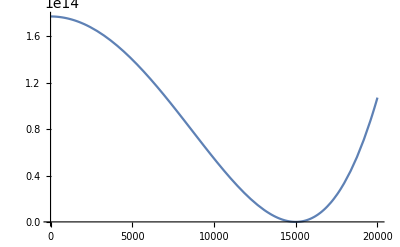

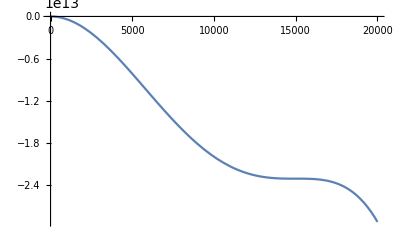

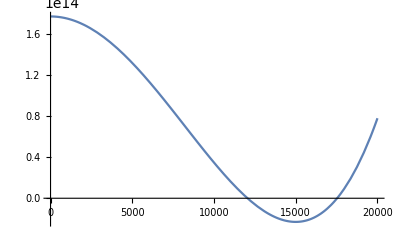

```mathematica
λR=0.014;
vR=15000;
Vtree[ϕ_]:=λR(ϕ^2-vR^2)^2/4;
Plot[Vtree[ϕ],{ϕ,0,20000}]
Clear[gR,gX,mZL,mWL,mBL,mW,mZ];
gR=1.55;
gX=√(gR^2 0.36^2/(gR^2-0.36^2));
mZL[ϕ_,T_]:=1/24 (3 gX^2 (13 T^2+ϕ^2)+gR^2 (26 T^2+3 ϕ^2)+√(-156 gR^2 gX^2 T^2 (26 T^2+5 ϕ^2)+(13 (2 gR^2+3 gX^2) T^2+3 (gR^2+gX^2) ϕ^2)^2))
(*mZL[ϕ,T]*)
mBL[ϕ_,T_]:=1/24 (3 gX^2 (13 T^2+ϕ^2)+gR^2 (26 T^2+3 ϕ^2)-√(-156 gR^2 gX^2 T^2 (26 T^2+5 ϕ^2)+(13 (2 gR^2+3 gX^2) T^2+3 (gR^2+gX^2) ϕ^2)^2))
(*mBL[ϕ,T]*)
Clear[yN3,yN2];
yN3=1.35;
yN2=0.89;
mN3[ϕ_]:=yN3^2 ϕ^2/2;
mN2[ϕ_]:=yN2^2 ϕ^2/2;
mZ[ϕ_]:=(gR^2+gX^2)ϕ^2/4;
mW[ϕ_]:=gR^2 ϕ^2/4;
mWL[ϕ_,T_]:=gR^2 ϕ^2/4+13/6 gR^2 T^2;
Clear[B,VCWren]
B=3/(64 π^2)(gR^4/8+((gR^2+gX^2)^2)/16-1/3 yN3^4-1/3 yN2^4);
VCWren[ϕ_]:=2B vR^2 ϕ^2-3/2 B ϕ^4+B ϕ^4 Log[ϕ^2/vR^2];
Plot[VCWren[ϕ],{ϕ,0,20000}]
Plot[Vtree[ϕ]+VCWren[ϕ],{ϕ,0,20000}]
```

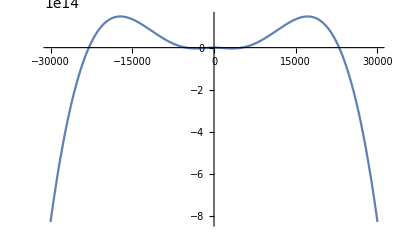

```mathematica
JB[x_]:=NIntegrate[z^2*Log[1-Exp[-Sqrt[z^2+x]]],{z,0,Infinity}]
(*bosonic field contributions*)
JF[x_]:=NIntegrate[z^2*Log[1+Exp[-Sqrt[z^2+x]]],{z,0,Infinity}]
(*fermionic field contributions*)
JBfit[x_]:=-Sum[(+1)^(1+j)*(x/j^2)*BesselK[2,j*Sqrt[x]],{j,1,20}]
JFfit[x_]:=Sum[(-1)^(1+j)*(x/j^2)*BesselK[2,j*Sqrt[x]],{j,1,20}]
(*Plot[{JBfit[x]-JB[x]},{x,0,10}]
Plot[{JFfit[x]-JF[x]},{x,0,10}]*)
Clear[VFT,Vring]
VFT[ϕ_,T_]:=T^4/(2 π^2)(6JBfit[mW[ϕ]/T^2]+3JBfit[mZ[ϕ]/T^2]-4JFfit[mN3[ϕ]/T^2]-4JFfit[mN2[ϕ]/T^2]);
(*Finite temperature without counting the thermal mass correction*)
Vring[ϕ_,T_]:=T/(12π)(2(mW[ϕ]^(3/2)-mWL[ϕ,T]^(3/2))+(mZ[ϕ]^(3/2)-mZL[ϕ,T]^(3/2))-mBL[ϕ,T]^(3/2))
(*Daisy resummation term for *)
Clear[Vtot];
Vt[ϕ_,T_]:=Vtree[ϕ]+VCWren[ϕ]+VFT[ϕ,T]+Vring[ϕ,T]
Vtot[ϕ_,T_]:=Vt[ϕ,T]-Vt[10^(-10),T]
Vbounce[ϕ_,T_]:=Vtot[ϕ,T]/;ϕ≥0
Vbounce[ϕ_,T_]:=Vtot[-ϕ,T]/;ϕ<0
Plot[-Vbounce[ϕ,4340],{ϕ,-30000,30000}]
```

17190.7

-1.48332×10^14

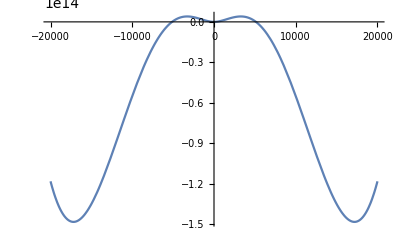

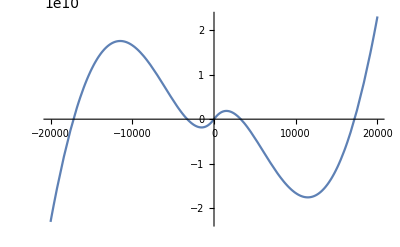

......................

NIntegrate::ncvb: NIntegrateが{AnyBubble`Private`r} = {3.0207}の近傍のAnyBubble`Private`rで二分法を7回反復しましたが，指定された確度に収束しませんでした．NIntegrateは積分と誤差推定として0.338603と3.31995×10^-7を得ました．

134.508

```mathematica
T1=4340;
fitting=Table[{ϕ,Vbounce[ϕ,T1]},{ϕ,1,20000,50}];
Vfit[ϕ_]=Fit[fitting,{1,ϕ,ϕ^2,ϕ^3,ϕ^4,ϕ^5,ϕ^6,ϕ^7,ϕ^8,ϕ^9,ϕ^10,ϕ^11,ϕ^12,ϕ^13,ϕ^14,ϕ^15,ϕ^16,ϕ^17,ϕ^18,ϕ^19,ϕ^20},ϕ];
Vb[ϕ_]:=Vfit[ϕ]/;ϕ≥0
Vb[ϕ_]:=Vfit[-ϕ]/;ϕ<0
xr=x/.Minimize[{Vfit[x],{13000<x<20000}},x][[2]]
ΔV=Minimize[{Vfit[v]-Vfit[0],{13000<v<20000}},v][[1]]
Plot[Vb[ϕ],{ϕ,-20000,20000}]
dVfit[ϕ_]:=Vfit'[ϕ]/;ϕ>=0
dVfit[ϕ_]:=-Vfit'[-ϕ]/;ϕ<0
Plot[dVfit[x],{x,-20000,20000}]
SbyT=(FindBubble[Vfit[x[1]]-Vfit[0],x,{xr},{0}]/T1)[[1]]
```

```mathematica
Clear[rinfty,bounceaction]
yIRcutoff=10^(-10);
rIRcutoff=10^(-10);
thickness=0.01;
shootinginitial=1000;
shootingfinal=24000;
δx0=10^(3);
δx1=10^(2);
δx2=10^(1);
δx3=10^(0);
δx4=10^(-1);
δx4=10^(-2);
δx5=10^(-3);
δt=thickness*10^(-1);
initialfun[y0_]:=Catch[Do[If[NDSolveValue[{(y''[x]+2/x y'[x])-dVfit[y[x]]==0,y[yIRcutoff]==y0
,y'[yIRcutoff]==0},y,{x,rIRcutoff,thickness}][t]<0,Throw[t]],{t,rIRcutoff,thickness,δt}]]
initial00=
Catch[Do[If[initialfun[y0]>0,Throw[y0]],{y0,shootinginitial,xr-.001,δx0}]]
initial11=
Catch[Do[If[initialfun[y0]>0,Throw[y0]],{y0,initial00-δx0,shootingfinal,δx1}]]
initial22=
Catch[Do[If[initialfun[y0]>0,Throw[y0]],{y0,initial11-δx1,shootingfinal,δx2}]]
initial33=Catch[Do[If[initialfun[y0]>0,Throw[y0]],{y0,initial22-δx2,shootingfinal,δx3}]]
initial44=Catch[Do[If[initialfun[y0]>0,Throw[y0]],{y0,initial33-δx3,shootingfinal,δx4}]]
initialf=Catch[Do[If[initialfun[y0]>0,Throw[y0]],{y0,initial44-δx4,shootingfinal,δx5}]]
rinfty[initialff_]:=Catch[Do[If[NDSolveValue[{(y''[x]+2/x y'[x])-dVfit[y[x]]==0,y[yIRcutoff]==initialff
,y'[yIRcutoff]==0},y,{x,rIRcutoff,thickness}][t]<0,Throw[t]],{t,rIRcutoff,thickness,δt}]]
bounceaction[initial_,rinfinity_]:=NIntegrate[Evaluate[4*Pi*x^2*((1/2)*y'[x]*y'[x]+Vfit[y[x]])/.NDSolve[{(y''[x]+2/x*y'[x])-dVfit[y[x]]==0,y[yIRcutoff]==initial
,y'[yIRcutoff]==0},y,{x,rIRcutoff,rinfinity}]],{x,10^(-10),rinfinity}]/(T1)
rinfty[initialf]
bounceaction[initialf,rinfty[initialf]]
```

13000

12200

12160

12157

303902/25

12156077/1000

0.009

{131.004}

1462.2

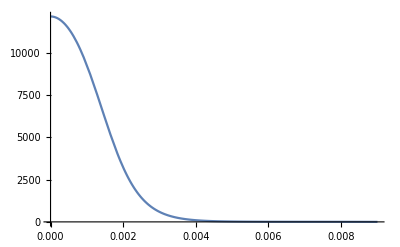

```mathematica
T1*(131.43484309407745-131.0979295522508)
(*beta parameter*)
Plot[NDSolveValue[{(y''[x]+2/x y'[x])-dVfit[y[x]]==0,y[rIRcutoff]==initialf,y'[rIRcutoff]==0},y[t],{x,10^(-10),thickness}],{t,rIRcutoff,rinfty[initialf]}]
(*wall configuration*)
```